## TemplateRandomSemicircularGrid-example.nb

Example Cellzilla2D notebook.

GPL License applies. 
See http://xlr8r.info and http://cellzilla.info for further details.

```mathematica
<<Cellzilla2D.m
```

Cellzilla2D (3.0.51h (15 June 2017)) loaded Sun 18 Jun 2017 08:54:08
using xCellerator 0.95 and XSSA 1.3.2
GPL License Terms Apply

Create a tissue with a point and an edge that aren't used.

There are 134 cells in the tissue.

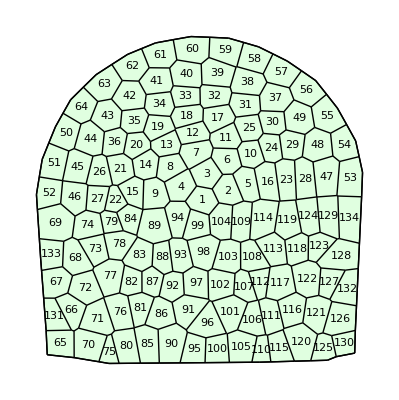

```mathematica
q=TemplateRandomSemicircularGrid[60, 100, 5];
Print["There are ", NTissueCells[q], " cells in the tissue."];  
ShowTissue[q, "CellNumbers"-> True]
```